# Open Quantum System

Harsh Mehta (m23iqt011@iitj.ac.in)

## The Beginning : Entangled State Generation and Verification

### Entangled State Generation

The ψ^- Bell state is a member of the set of four Bell states, which are quantum states that are maximally entangled. These states demonstrate a flawless correlation between the spins of two entangled particles, irrespective of their physical distance. The ψ^- Bell state exhibits perfect negative correlation between the entangled qubits. When one qubit is measured to be in the state 0 the other qubit is guaranteed to be in the state 1, and vice versa.
We Initially Assume that ,the Bell Stateψ^- = 1/(√2)[01-10] is shared between Alice and Bob at t=0.
Density Matrix for the state is given by ρ(t=0).

```mathematica
<<Wolfram`QuantumFramework`;
SetQuantumAlises[];
Ket0={{1},{0}};
Ket1={{0},{1}} ;
01=KroneckerProduct[Ket0,Ket1];
10=KroneckerProduct[Ket1,Ket0];
00=KroneckerProduct[Ket0,Ket0];
11=KroneckerProduct[Ket1,Ket1];
QState =(1/(√2)(01-10));
ρZero = QState.ConjugateTranspose[QState];
Print["Density Matrix of the state ψ^- is ρ(t=0) = ",MatrixForm[ρZero]];
```

Density Matrix of the state ψ^- is ρ(t=0) = (0 | 0 | 0 | 0
0 | 1/2 | -1/2 | 0
0 | -1/2 | 1/2 | 0
0 | 0 | 0 | 0)

### State Verification

#### Valid Quantum State Verification (Coherence)

Coherence refers to the ability of a quantum system to maintain phase relationships between different quantum states, allowing for interference effects and the preservation of superposition properties.
It is defined as C(ρ) = ∑_(i≠j) |ρ_ij| Here ρ_ij represents off-diagonal elements-of density matrix ρ and the sum is taken over all pairs of off-diagonal elements ρ_ij, where i≠j.

```mathematica
Coherence = Simplify[Abs[ρZero[[4,1]] + ρZero[[3,2]]+ρZero[[2,3]]+ρZero[[1,4]]],Element[_,Reals]];
Print["Coherence of  the state ψ^- at t=0 is =",Coherence ]
```

Coherence of  the state ψ^- at t=0 is =1

Since, value of Coherence is 1, it indicates a valid quantum state is generated involving the two qubits.

#### Maximally Entangled State Verification (Concurrence)

Concurrence is a valuable measure of entanglement in mixed states, where entanglement can coexist with classical correlations or noise. The range of values for entanglement spans from 0, which represents separable states with no entanglement, to 1, which represents maximally entangled states. Thus, it quantifies the extent of non-local correlations existing in the system.
For a two-qubit state represented by a density matrix ρ, the concurrence C(ρ) is defined as follows:
C(ρ) = max(0,√e_1-√e_2 -√e_3-√e_4)
Where e_i are the square roots of the eigenvalues of the matrix R = ρ (σ_y ⊗ σ_y) ρ^* (σ_y ⊗ σ_y) arranged in decreasing order. Here ρ^* represents the complex conjugate of ρ, and σ_y is Pauli Y matrix.

```mathematica
Subscript[σ, y] ={{0,-I},{I,0}};
Eg=Sort[Eigenvalues[ρZero.KroneckerProduct[Subscript[σ, y],Subscript[σ, y]].Transpose[ρZero].KroneckerProduct[Subscript[σ, y],Subscript[σ, y]]]];
Con = FullSimplify[Max[0,Sqrt[{Eg[[4]]- Eg[[3]]-Eg[[2]]-Eg[[1]]}]]];
Print["Concurrence C(ρ(t=0)) = ", Con]
```

Concurrence C(ρ(t=0)) = 1

As, Concurrence of state ψ^-(t=0)is 1, it implies that Generated state is maximally Entangled state at t=0.

## Amplitude Damping (AD) and Generalized Amplitude Damping (GAD) Channel

### Introduction

#### Amplitude Damping (AD) Channel

The Amplitude Damping Channel is a quantum noise channel that represents the dissipation of energy from a quantum system to its surroundings, resulting in the decay of the system’s amplitude. This particular type of channel is frequently encountered in the field of quantum information processing, particularly in systems that are susceptible to decoherence.The Amplitude Damping Channel refers to the phenomenon where a qubit undergoes interaction with its surrounding environment, resulting in the depletion of amplitude or energy from the qubit’s state. This loss can arise from different physical mechanisms, such as the emission of photons in a quantum optical system or the emission of phonons in a solid-state system.
	When the qubit is initially in the excited state ∣1⟩, the amplitude damping channel leads to a reduction in the probability amplitude of this state as time progresses. Ultimately, the qubit may ultimately transition to the ground state ∣0⟩ as a result of the damping process. This may result in the process of “Decoherence” which occurs when the amplitude damping channel causes the loss of quantum coherence between different states of the qubit. The lack of coherence impairs the capacity to carry out quantum computations or communication with reliability, as the quantum information becomes vulnerable to errors. It is also associated with  effect of  “Dephasing” which refers to the alteration of the relative phase between different components of the qubit’s state, which can be induced by the damping process. This dephasing additionally contributes to the deterioration of quantum coherence and accuracy of quantum operations.
	The amplitude damping channel is commonly characterized using a Kraus representation. The Kraus operators for the Amplitude Damping channel are denoted as 𝐾_i where i  ranges from 0 to 1. Each Kraus operator represents a possible quantum transition that the qubit can undergo under the influence of the channel.

"K0 = "(1 | 0
0 | √(1-λ))", K0^† ="(1 | 0
0 | √(1-λ))
Here, λ Represents the probability of the qubit experiencing damping, which corresponds to the loss of amplitude (or energy) to the environment. Here, λ = 1 - e^-γ_0t, where γ_0 is the damping rate and t is the time of evolution. 

 "K1 = "(0 | √λ
0 | 0)", K1^† ="(0 | 0
√λ | 0)	 
Describes the scenario where the qubit gains energy from the environment and transitions from the ground state to the excited state. The factor √λ represents the probability amplitude of this excitation process. The effects of amplitude damping can be represented visually as a flow on the Bloch sphere.

```mathematica
generateBlochSphere[h_,title_]:=Module[{blochVectorsM,scalingFactor},blochVectorsM={{1*Simplify[Sqrt[1-(1-Exp[-h])]],0,0},{0,1*Simplify[Sqrt[1-(1-Exp[-h])]],0},{0,0,Simplify[(1-Exp[-h])+1*(1-(1-Exp[-h]))]}};
scalingFactor=Max[blochVectorsM[[All,1]]];
Graphics3D[{{Opacity[0.5],Gray,Sphere[{0,0,0},1]},{Blue,Tube[{{0,0,-1},{0,0,1}},0.05]},{Red,Scale[Sphere[{0,0,0},1],{scalingFactor,scalingFactor,1}]},Arrow[{{0,0,0},#}]&/@blochVectorsM,{PointSize[Large],Point[{0,0,0}]}},Boxed->False,Axes->True,Ticks-> None,AxesLabel->{"X","Y","Z"},PlotRange->{{-1,1},{-1,1},{-1,1}},ImageSize->Medium,PlotLabel->Style[title,Bold,14]]]
GraphicsRow[{generateBlochSphere[0.2,"γ_0 = 0.2"],generateBlochSphere[0.4,"γ_0 = 0.4"],generateBlochSphere[0.6,"γ_0 = 0.6"],generateBlochSphere[0.8,"γ_0 = 0.8"]}]
```

-Graphics-

Each Bloch sphere represents the state of a quantum system after undergoing amplitude damping with a specific damping parameter.

#### Generalized Amplitude Damping (GAD) Channel

The Generalized Amplitude Damping Channel expands upon the Amplitude Damping Channel by incorporating supplementary effects, such as the environment gaining energy. In the Generalized Amplitude Damping Channel, in addition to the energy loss from the qubit to the environment, there are processes in which the environment acquires energy while the qubit loses energy. These processes cause an imbalance in the damping dynamics.
	The Generalized Amplitude Damping Channel differs from the Amplitude Damping Channel by taking into account both energy loss and energy gain processes, whereas the Amplitude Damping Channel only considers the loss of energy from the qubit to the environment. The lack of symmetry in this situation results in a more intricate damping process, where the qubit’s state can experience transitions that involve both decay and excitation. The GAD channel incorporates supplementary parameters, such as the excitation rate, which determines the likelihood of the qubit acquiring energy from its surroundings. These parameters have an impact on the development of the qubit’s state, leading to a wider range of potential changes, such as decay, excitation, and dephasing.
		Similar to other quantum channels, the Generalized Amplitude Damping Channel is typically described using a set of Kraus operators that capture the evolution of the qubit’s state under the influence of the channel. The Kraus operators for the GAD channel are denoted as E_i where i ranges from 0 to 3. Each Kraus operator represents a possible quantum transition that the qubit can undergo under the influence of the channel.

"E0 = "(√p | 0
0 | √p √(1-α))", E0^† ="(√p | 0
0 | √p √(1-α))
Here, p Represents the probability of the qubit experiencing damping, corresponding to the loss of energy to the environment. Here, α Represents the probability of the qubit gaining energy from the environment and undergoing excitation. Here,  α = 1 - e^-γt, where γ = γ_0(2N+1) , and N =  1/(e^(ℏω/(k_β T))-1)  Is Bose-Einstein Distribution. For Simplicity we assume, ℏω/k_β = 1. This Describes the scenario where the qubit remains in the same state (either ground or excited) without undergoing excitation. The factor √(1 - α) represents the preservation of the qubit’s state due to the damping process.

"E1 = "(0 | √p √α
0 | 0)", E1^† ="(0 | 0
√p √α | 0)
This Describes the scenario where the qubit gains energy from the environment and transitions from the ground state to the excited state. The factor √α represents the probability amplitude of this excitation process.

"E2 = "(√(1-p) √(1-α) | 0
0 | √(1-p))", E2^† ="(√(1-p) √(1-α) | 0
0 | √(1-p))
1 - p, Represents the probability of the qubit not experiencing damping, i.e., remaining in its current state without undergoing damping. This Describes the scenario where the qubit remains in its current state without undergoing excitation. The factors √(1 - α) ensure the preservation of the qubit’s state due to the absence of damping.

"E3 = "(0 | 0
√(1-p) √α | 0)", E3^† ="(0 | √(1-p) √α
0 | 0)
Describes the scenario where the qubit gains energy from the environment and transitions from the ground state to the excited state. The factor √α represents the probability amplitude of this excitation process.

## Effect of Various Channels on Time Evolution of State ψ^-

### Case - I : AD on Alice’s Qubit and GAD on Bob’s Qubit

#### Density Matrix Evolution under Effect of Channels

After a certain duration of time, the condition of the two qubits will have changed as a result of the impact of amplitude damping (AD) on Alice’s qubit and generalized amplitude damping (GAD) on Bob’s qubit. Let us examine the current state of the system. 
The evaluation of State in terms of Density matrix can be characterized by Kraus operators corresponding to different Operators, defined as...
ρ(t) = ∑_(i=0)^1 ∑_(j=0)^3  (K_i ⊗ E_j) ρ(0) (K_i^† ⊗ E_j^†)

```mathematica
K0 = {{1,0},{0,Sqrt[(1-λ)]}};
K0D = Simplify[ConjugateTranspose[K0],Element[_,Reals]];
K1 = {{0,Sqrt[λ]},{0,0}};
K1D = Simplify[ConjugateTranspose[K1],Element[_,Reals]];
E0 = (Sqrt[p]){{1,0},{0,Sqrt[(1-α)]}};
E0D =Simplify[ConjugateTranspose[E0],Element[_,Reals]];
E1 = (Sqrt[p]){{0,Sqrt[α]},{0,0}};
E1D = Simplify[ConjugateTranspose[E1],Element[_,Reals]];
E2 = (Sqrt[1-p]){{Sqrt[(1-α)],0},{0,1}};
E2D = Simplify[ConjugateTranspose[E2],Element[_,Reals]];
E3 = (Sqrt[1-p]){{0,0},{Sqrt[α],0}};
E3D = Simplify[ConjugateTranspose[E3],Element[_,Reals]];
KO={K0,K1};
KD={K0D,K1D};
EO={E0,E1,E2,E3};
ED={E0D,E1D,E2D,E3D};

ρTime=Sum[KroneckerProduct[KO[[i]],EO[[j]]].ρZero.KroneckerProduct[KD[[i]],ED[[j]]],{i,1,Length[KO]},{j,1,Length[EO]}];
Print["Density Matrix ρ(t=t) = ",MatrixForm[FullSimplify[ρTime]],"; Tr[ρ(t=t)] = ",FullSimplify[Tr[ρTime]]]
```

Density Matrix ρ(t=t) = (1/2 (λ+α (p+(-1+p) λ)) | 0 | 0 | 0
0 | 1/2 (1+α λ-p α (1+λ)) | -1/2 √(1-α) √(1-λ) | 0
0 | -1/2 √(1-α) √(1-λ) | -1/2 (1+(-1+p) α) (-1+λ) | 0
0 | 0 | 0 | 1/2 (-1+p) α (-1+λ)); Tr[ρ(t=t)] = 1

Notice that Trace of ρ(t) is 1.

#### Coherence of Time Evaluated State

As Alice’s qubit passes through AD, its coherence gradually decreases, and it becomes more similar to a classical system, losing the ability to maintain superposition and interference effects. Likewise, the qubit belonging to Bob that undergoes Generalized Amplitude Damping (GAD) undergoes a loss of coherence. The presence of GAD amplifies the loss of coherence, resulting in a more rapid decay of quantum correlations in Bob’s qubit compared to Alice’s.

Coherence of ρ(t) =Abs[√(1-α) √(1-λ)]

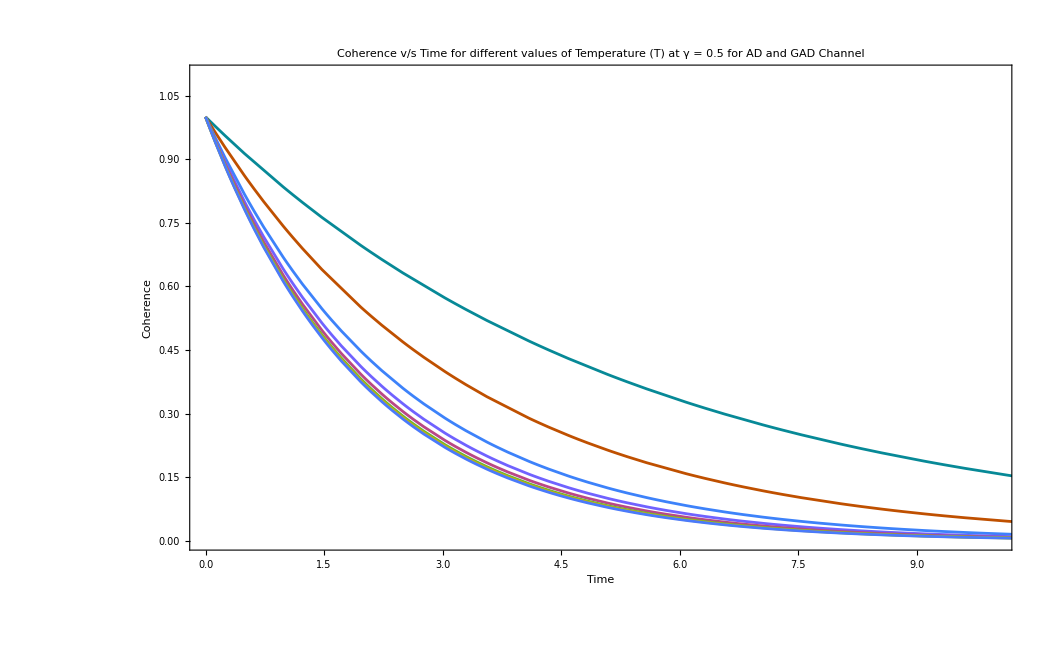

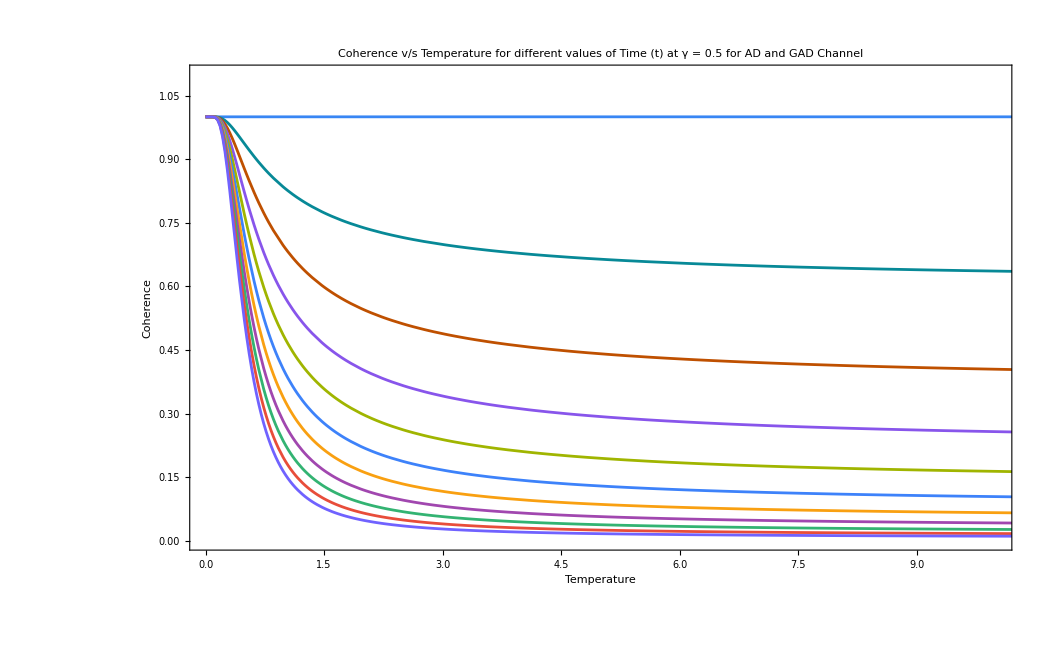

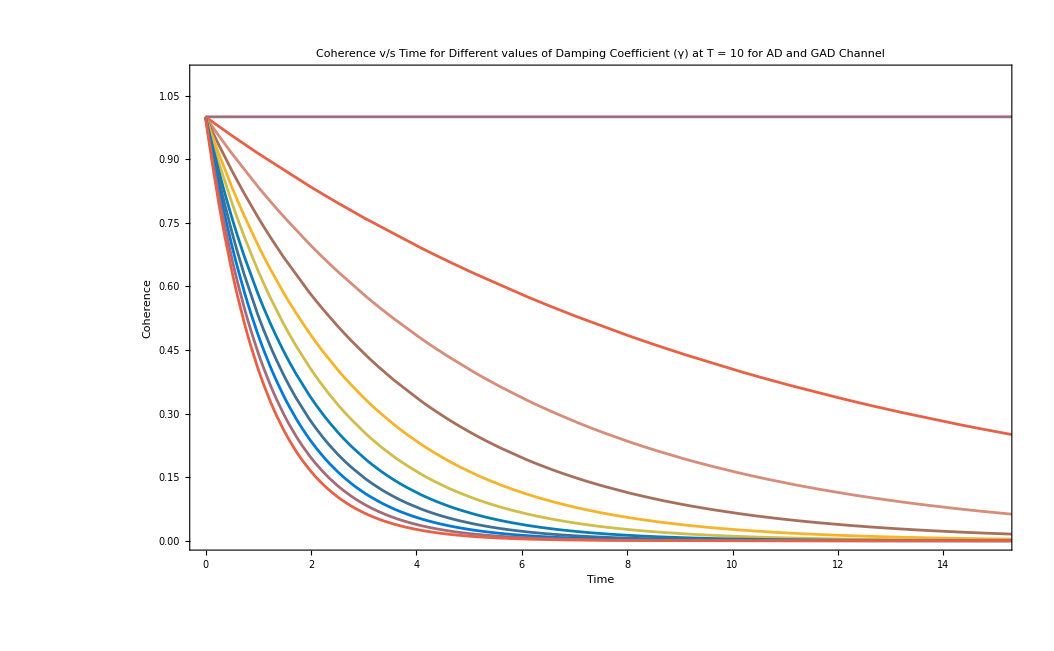

```mathematica
CoherenceT = Simplify[Abs[ρTime[[4,1]] + ρTime[[3,2]]+ρTime[[2,3]]+ρTime[[1,4]]],Element[_,Reals]];
Print["Coherence of ρ(t) =", CoherenceT]
λ = Simplify[1 - Exp[-h*t],Element[_,Reals]];
α = Simplify[1-Exp[-h*(2(1/Exp[1/T]-1)+1)*t],Element[_,Reals]];
p = FullSimplify[((1/(Exp[1/T]-1))+1)/(2*(1/(Exp[1/T]-1))+1),Element[_,Reals]];

CoherenceT;

Show[Table[Plot[CoherenceT /. h-> 0.5,{t,0,100},PlotRange->{{0,10},{0,1.1}},Frame->True,FrameStyle->Directive[Black,Thin],PlotStyle->ColorData[104][T],PlotLegends->Placed[{"T = "<>ToString[T]},{Center,Top}],FrameLabel->{"Time","Coherence"},PlotLabel->"Coherence v/s Time for different values of Temperature (T) at γ = 0.5 for AD and GAD Channel"],{T,{1,2,5,10,20,50,100,1000}}]]
Show[Table[Plot[CoherenceT /. h-> 0.5,{T,0,100},PlotRange->{{0,10},{0,1.1}},Frame->True,FrameStyle->Directive[Black,Thin],PlotStyle->ColorData[104][t],PlotLegends->Placed[{"t = "<>ToString[t]},{Center,Top}],FrameLabel->{"Temperature","Coherence"},PlotLabel->"Coherence v/s Temperature for different values of Time (t) at γ = 0.5 for AD and GAD Channel"],{t,0,10,1}]]
Show[Table[Plot[CoherenceT /. T-> 10,{t,0,100},PlotRange->{{0,15},{0,1.1}},Frame->True,FrameStyle->Directive[Black,Thin],PlotStyle->ColorData[28][10*h],PlotLegends->Placed[{"γ = "<>ToString[h]},{Center,Top}],FrameLabel->{"Time","Coherence"},PlotLabel->"Coherence v/s Time for Different values of Damping Coefficient (γ) at T = 10 for AD and GAD Channel"],{h,0,1,0.1}]]
λ=.;
α=.;
p=.;
h=.;
T=.;
CoherenceT=.;
```

#### Concurrence of Time Evaluated State

Amplitude damping and generalized amplitude damping result in a decrease in the concurrence of a Bell state by inducing the loss of quantum coherence and entanglement between the qubits. The decrease in Concurrence is a result of environmental interactions on the entangled state of the qubits.

Concurrence C(ρ(t=t)) = 1/2 (-2 √((-1+p) α (-1+λ) (λ-α λ+p α (1+λ)))+√(α (-1+λ) (2+(-1+p) λ)+(-1+p) α^2 (-1+λ) (p-λ+p λ)+2 (1-λ+√((-1+α) (1+(-1+p) α) (-1+λ)^2 (-1-α λ+p α (1+λ)))))-√(α (-1+λ) (2+(-1+p) λ)+(-1+p) α^2 (-1+λ) (p-λ+p λ)-2 (-1+λ+√((-1+α) (1+(-1+p) α) (-1+λ)^2 (-1-α λ+p α (1+λ))))))

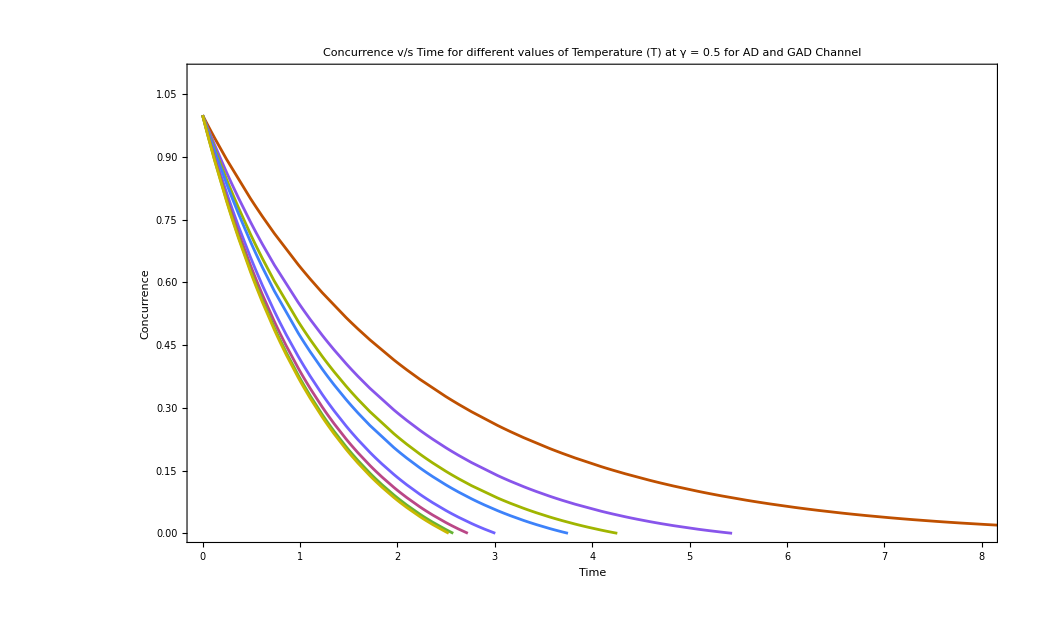

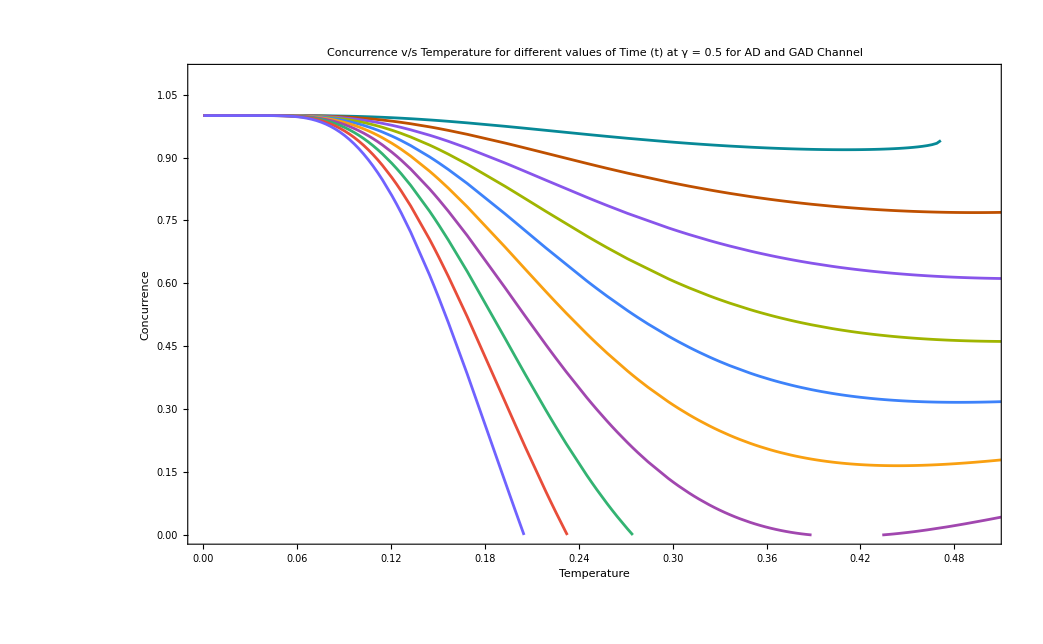

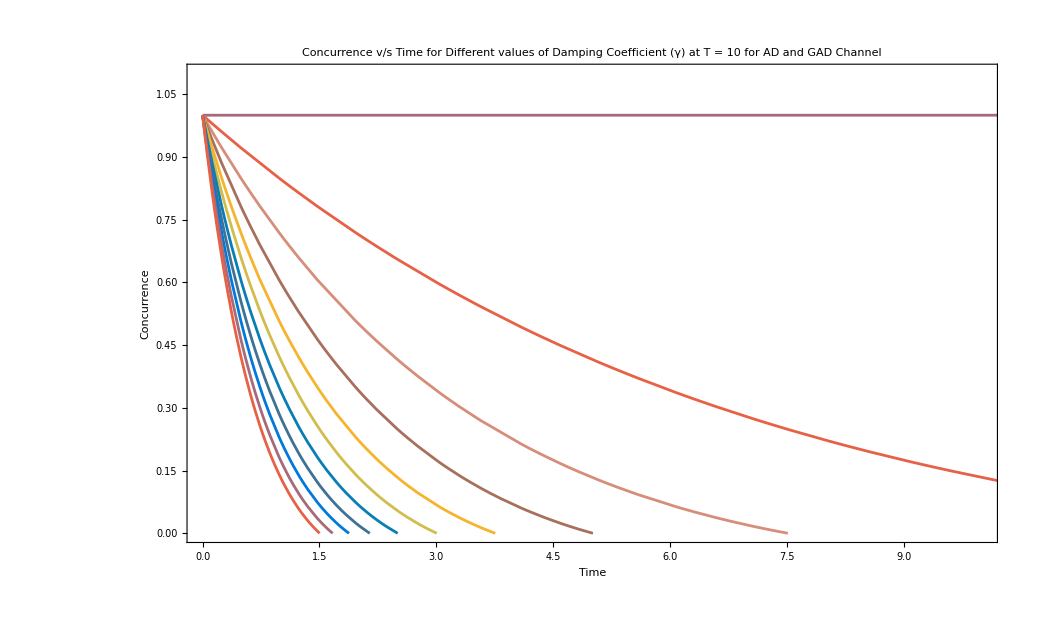

```mathematica
Subscript[σ, y] ={{0,-I},{I,0}};
Egg=KroneckerProduct[Subscript[σ, y],Subscript[σ, y]].Transpose[ρTime].KroneckerProduct[Subscript[σ, y],Subscript[σ, y]];
EgT = Sqrt[Sort[Eigenvalues[ρTime.Egg]]];
ConT = Simplify[EgT[[4]]- EgT[[3]]-EgT[[2]]-EgT[[1]]];
Print["Concurrence C(ρ(t=t)) = ", ConT]

λ = 1 - Exp[-h*t];
α = Simplify[1 - Exp[-h*(2(1/Exp[1/T]-1)+1)*t]];
p = Simplify[((1/(Exp[1/T]-1))+1)/(2*(1/(Exp[1/T]-1))+1)];

ConT;

Show[Table[Plot[ConT/.h->0.5,{t,0,100},PlotRange->{{0,8},{0,1.1}},Frame->True,FrameStyle->Directive[Black,Thin],PlotStyle->ColorData[104][T],
PlotLegends->Placed[{"T = "<>ToString[T]},{Center,Top}],FrameLabel->{"Time","Concurrence"},
PlotLabel->"Concurrence v/s Time for different values of Temperature (T) at γ = 0.5 for AD and GAD Channel"],{T,{2,3,4,5,10,20,50,100}}]]

Show[Table[Plot[ExpandAll[ConT/.h->0.5],{T,0,100},PlotRange->{{0,0.5},{0,1.1}},PlotPoints->500,Frame->True,FrameStyle->Directive[Black,Thin],PlotStyle->ColorData[104][t],
PlotLegends->Placed[{"t = "<>ToString[t]},{Center,Top}],FrameLabel->{"Temperature","Concurrence"},
PlotLabel->"Concurrence v/s Temperature for different values of Time (t) at γ = 0.5 for AD and GAD Channel"],{t,1,10,1}]]

Show[Table[Plot[ConT/.T->10,{t,0,100},PlotRange->{{0,10},{0,1.1}},Frame->True,FrameStyle->Directive[Black,Thin],PlotStyle->ColorData[28][10*h],
PlotLegends->Placed[{"γ = "<>ToString[h]},{Center,Top}],FrameLabel->{"Time","Concurrence"},
PlotLabel->"Concurrence v/s Time for Different values of Damping Coefficient (γ) at T = 10 for AD and GAD Channel"],{h,0,1,0.1}]]

λ=.;
α=.;
p=.;
h=.;
T=.;
ConT=.;
```

#### Fidelity of Time Evaluated State with State at t = 0

The fidelity between the ideal Bell state and the state after amplitude damping or generalized amplitude damping does not diminish completely to zero due to the presence of residual coherence and correlation between the qubits in the resulting state. This primarily occurs as a result of the influence of Generalized Amplitude Damping (GAD), which induces a state of heightened stimulation.
Fidelity between ρ(t=0) and ρ(t=t) is

Fidelity f(ρ(t),ρ(0)) = 1/2 √(2+2 √(1-α) √(1-λ)-λ+α (-1-2 (-1+p) λ))

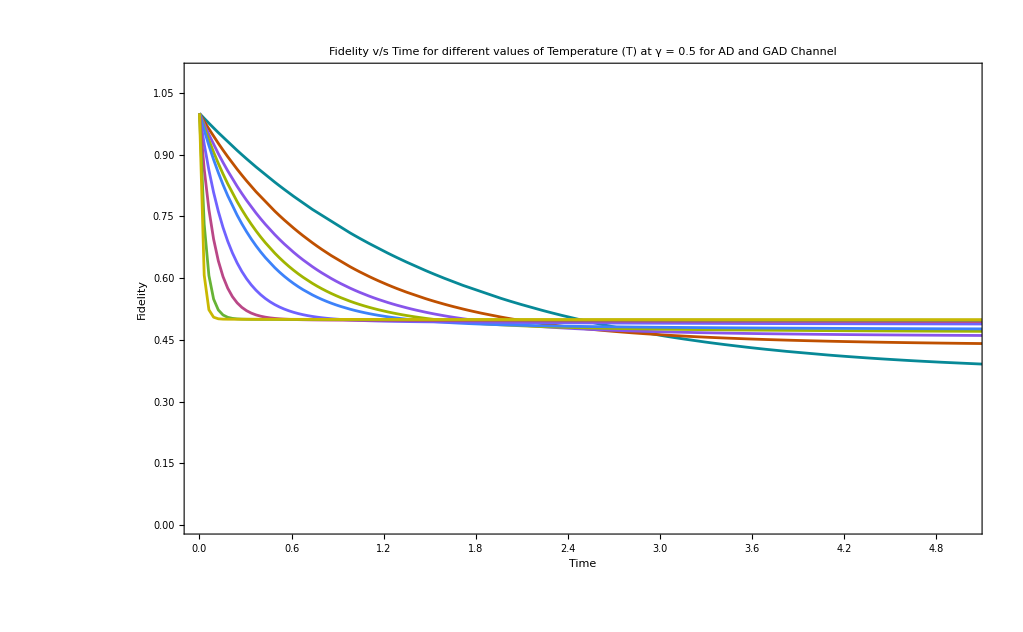

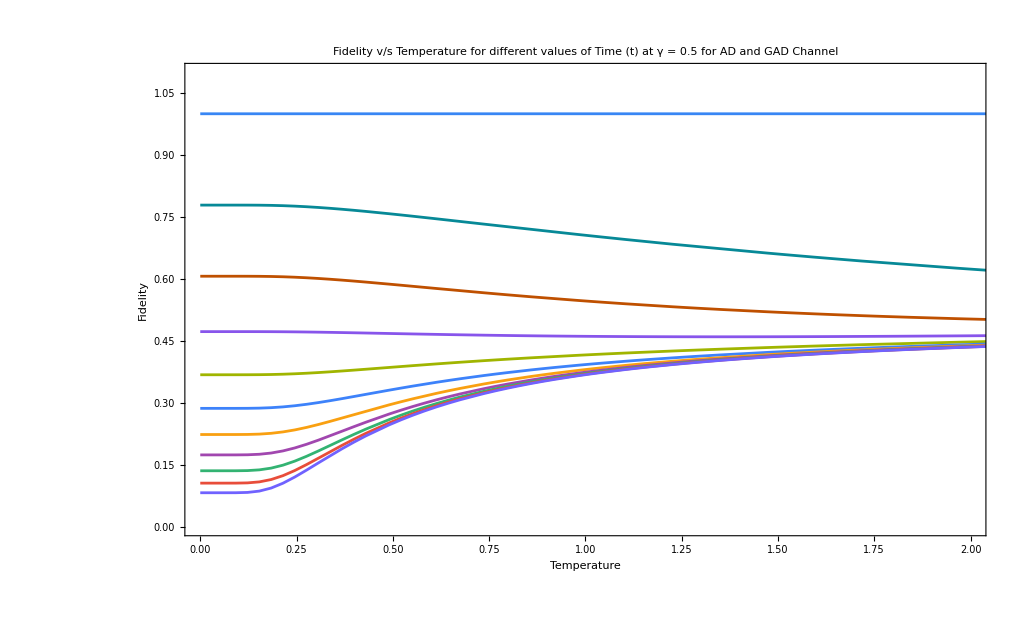

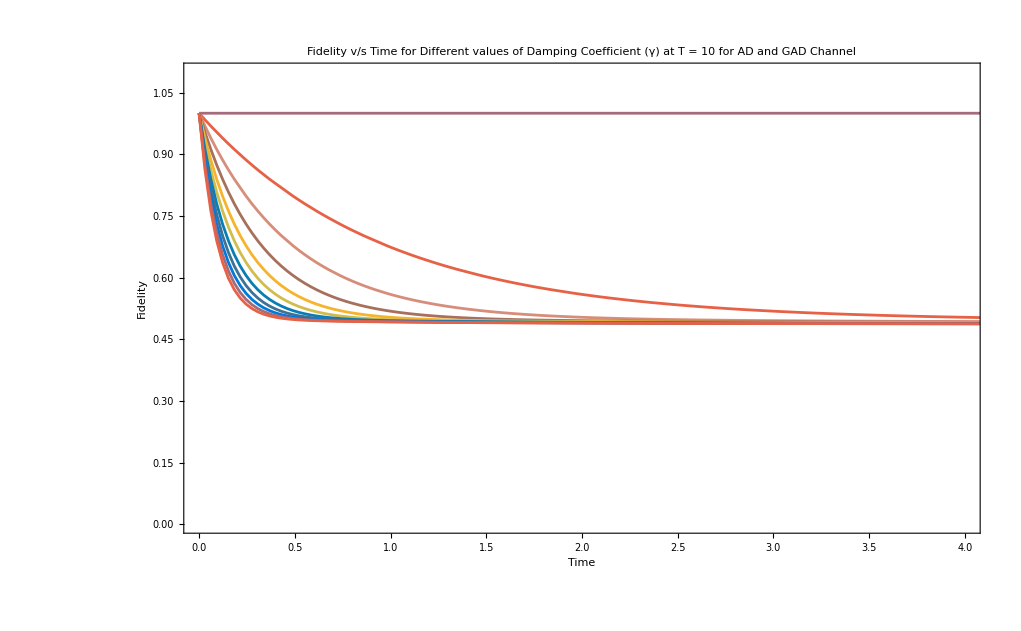

```mathematica
Fidelity = FullSimplify[Tr[MatrixPower[MatrixPower[ρZero,1/2].ρTime.MatrixPower[ρZero,1/2],1/2]]];
Print["Fidelity f(ρ(t),ρ(0)) = ",Fidelity]
λ = 1 - Exp[-h*t];
α = Simplify[1-Exp[-h*(2(1/(Exp[1/T]-1))+1)*t]];
p = Simplify[((1/(Exp[1/T]-1))+1)/(2*(1/(Exp[1/T]-1))+1)];

Fidelity;

ff[t_,T_]:=FullSimplify[Fidelity /. h-> 0.5];
Show[Table[Plot[Fidelity /. h-> 0.5,{t,0,100},PlotRange->{{0,5},{0,1.1}},Frame->True,FrameStyle->Directive[Black,Thin],PlotStyle->ColorData[104][T],
PlotLegends->Placed[{"T = "<>ToString[T]},{Center,Top}],FrameLabel->{"Time","Fidelity"},
PlotLabel->"Fidelity v/s Time for different values of Temperature (T) at γ = 0.5 for AD and GAD Channel"],{T,{1,2,3,4,5,10,20,50,100}}]]

Show[Table[Plot[ExpandAll[Fidelity /. h-> 0.5],{T,0,100},PlotRange->{{0,2},{0,1.1}},Frame->True,FrameStyle->Directive[Black,Thin],PlotStyle->ColorData[104][t],
PlotLegends->Placed[{"t = "<>ToString[t]},{Center,Top}],FrameLabel->{"Temperature","Fidelity"},
PlotLabel->"Fidelity v/s Temperature for different values of Time (t) at γ = 0.5 for AD and GAD Channel"],{t,0,10,1}]]

Show[Table[Plot[Fidelity /. T-> 10,{t,0,100},PlotRange->{{0,4},{0,1.1}},Frame->True,FrameStyle->Directive[Black,Thin],PlotStyle->ColorData[28][10*h],
PlotLegends->Placed[{"γ = "<>ToString[h]},{Center,Top}],FrameLabel->{"Time","Fidelity"},
PlotLabel->"Fidelity v/s Time for Different values of Damping Coefficient (γ) at T = 10 for AD and GAD Channel"],{h,0,1,0.1}]]

λ=.;
α=.;
p=.;
h=.;
T=.;
Fidelity=.;
```

### Case - II : AD on Alice’s Qubit and AD on Bob’s Qubit

#### Density Matrix Evolution under Effect of Channels

After a certain duration of time, the condition of the two qubits will have changed as a result of the impact of amplitude damping (AD) on Alice’s qubit and amplitude damping (AD) on Bob’s qubit as well. Let us examine the current state of the system. 
The evaluation of State in terms of Density matrix can be characterized by Kraus operators corresponding to different Operators, defined as...
ρ(t) = ∑_(i=0)^1 ∑_(j=0)^1  (K_i ⊗ E_j) ρ(0) (K_i^† ⊗ E_j^†)

```mathematica
K0 = {{1,0},{0,Sqrt[(1-λ)]}};
K0D = Simplify[ConjugateTranspose[K0],Element[_,Reals]];
K1 = {{0,Sqrt[λ]},{0,0}};
K1D = Simplify[ConjugateTranspose[K1],Element[_,Reals]];
E0 = {{1,0},{0,Sqrt[(1-α)]}};
E0D =Simplify[ConjugateTranspose[E0],Element[_,Reals]];
E1 = {{0,Sqrt[α]},{0,0}};
E1D = Simplify[ConjugateTranspose[E1],Element[_,Reals]];

KO={K0,K1};
KD={K0D,K1D};
EO={E0,E1};
ED={E0D,E1D};

ρTime=Sum[KroneckerProduct[KO[[i]],KO[[j]]].ρZero.KroneckerProduct[KD[[i]],KD[[j]]],{i,1,Length[KO]},{j,1,Length[KO]}];
Print["Density Matrix ρ(t=t) = ",MatrixForm[FullSimplify[ρTime]],"; Tr[ρ(t=t)] = ",FullSimplify[Tr[ρTime]]]
```

Density Matrix ρ(t=t) = (λ | 0 | 0 | 0
0 | (1-λ)/2 | 1/2 (-1+λ) | 0
0 | 1/2 (-1+λ) | (1-λ)/2 | 0
0 | 0 | 0 | 0); Tr[ρ(t=t)] = 1

Notice that Trace of ρ(t) is 1.

#### Coherence of Time Evaluated State

As Alice’s qubit passes through AD, its coherence gradually decreases, and it becomes more similar to a classical system, losing the ability to maintain superposition and interference effects. Likewise, the qubit belonging to Bob that undergoes Generalized Amplitude Damping (GAD) undergoes a loss of coherence. The presence of GAD amplifies the loss of coherence, resulting in a more rapid decay of quantum correlations in Bob’s qubit compared to Alice’s.

Coherence of ρ(t) =Abs[-1+λ]

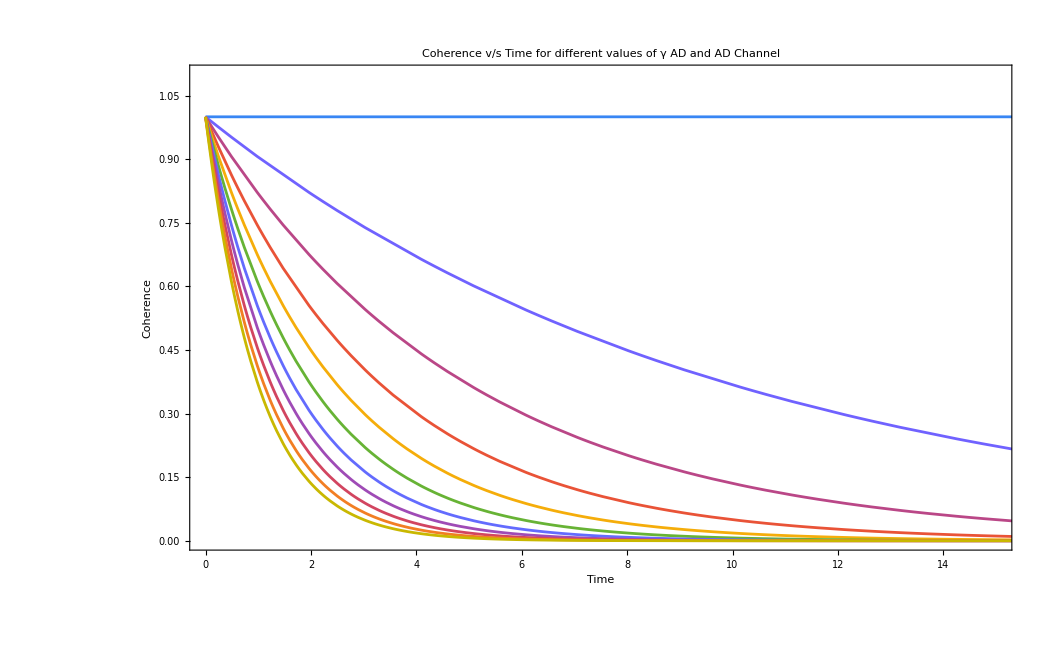

```mathematica
CoherenceT = Simplify[Abs[ρTime[[4,1]] + ρTime[[3,2]]+ρTime[[2,3]]+ρTime[[1,4]]],Element[_,Reals]];
Print["Coherence of ρ(t) =", CoherenceT]
λ = Simplify[1 - Exp[-h*t],Element[_,Reals]];

CoherenceT;


Show[Table[Plot[CoherenceT,{t,0,100},PlotRange->{{0,15},{0,1.1}},Frame->True,FrameStyle->Directive[Black,Thin],PlotStyle->ColorData[104][100*h],PlotLegends->Placed[{"γ = "<>ToString[h]},{Center,Top}],FrameLabel->{"Time","Coherence"},PlotLabel->"Coherence v/s Time for different values of γ AD and AD Channel"],{h,0,1,0.1}]]
λ=.;
h=.;
CoherenceT=.;
```

#### Concurrence of Time Evaluated State

When AD is applied to both qubits of a Bell state, it introduces decoherence and causes the entangled state to evolve towards a mixed state, which reduces the concurrence. As the damping parameter increases, the degree of entanglement decreases, leading to a reduction in concurrence.

Concurrence C(ρ(t=t)) = √((-1+λ)^2)

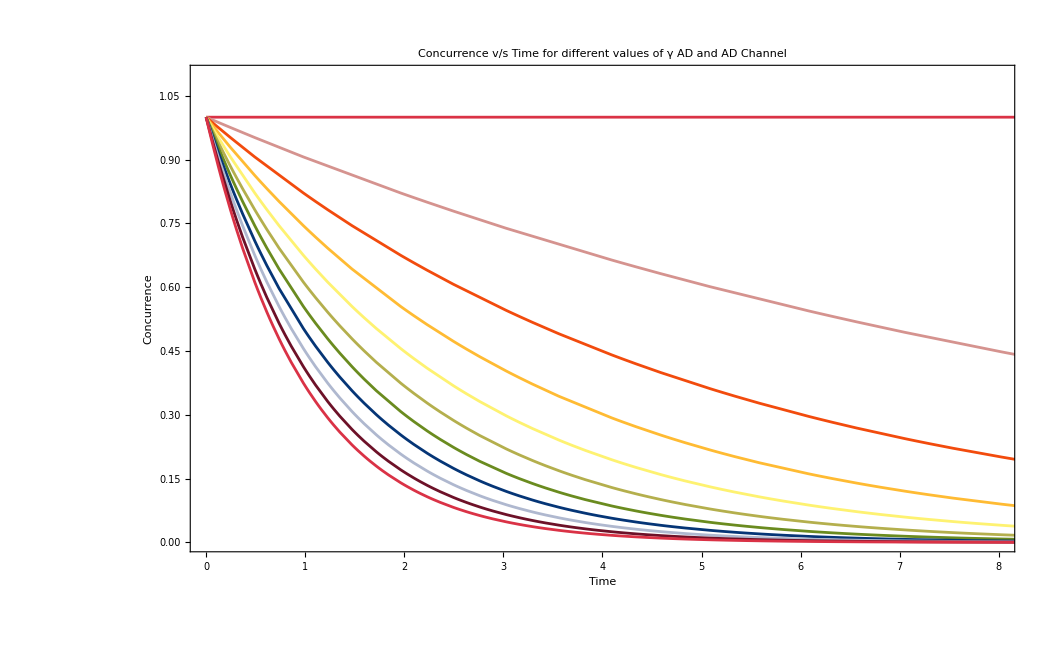

```mathematica
Subscript[σ, y] ={{0,-I},{I,0}};
Egg=KroneckerProduct[Subscript[σ, y],Subscript[σ, y]].Transpose[ρTime].KroneckerProduct[Subscript[σ, y],Subscript[σ, y]];
EgT = Sqrt[Sort[Eigenvalues[ρTime.Egg]]];
ConT = Simplify[EgT[[4]]- EgT[[3]]-EgT[[2]]-EgT[[1]]];
Print["Concurrence C(ρ(t=t)) = ", ConT]

λ = 1 - Exp[-h*t];

ConT;

Show[Table[Plot[ConT,{t,0,100},PlotRange->{{0,8},{0,1.1}},Frame->True,FrameStyle->Directive[Black,Thin],PlotStyle->ColorData[14][10*h],
PlotLegends->Placed[{"γ = "<>ToString[h]},{Center,Top}],FrameLabel->{"Time","Concurrence"},
PlotLabel->"Concurrence v/s Time for different values of γ AD and AD Channel"],{h,0,1,0.1}]]

λ=.;
h=.;
ConT=.;
```

#### Fidelity of Time Evaluated State with State at t = 0

AD introduces decoherence to both qubits, leading to the loss of quantum coherence and entanglement between them. As a result, the state after AD gradually becomes more mixed and less correlated with the ideal Bell state.
Fidelity between ρ(t=0) and ρ(t=t) is

Fidelity f(ρ(t),ρ(0)) = √(1-λ)

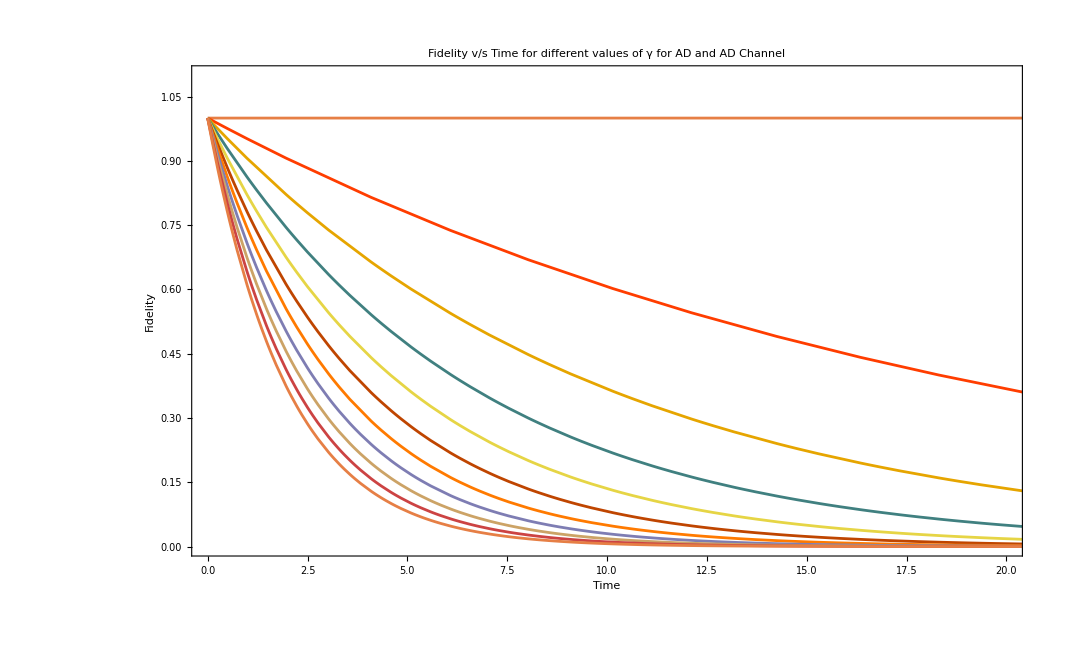

```mathematica
Fidelity = FullSimplify[Tr[MatrixPower[MatrixPower[ρZero,1/2].ρTime.MatrixPower[ρZero,1/2],1/2]]];
Print["Fidelity f(ρ(t),ρ(0)) = ",Fidelity]
λ = 1 - Exp[-h*t];

Fidelity;

Show[Table[Plot[Fidelity,{t,0,100},PlotRange->{{0,20},{0,1.1}},Frame->True,FrameStyle->Directive[Black,Thin],PlotStyle->ColorData[70][10*h],
PlotLegends->Placed[{"γ = "<>ToString[h]},{Center,Top}],FrameLabel->{"Time","Fidelity"},
PlotLabel->"Fidelity v/s Time for different values of γ for AD and AD Channel"],{h,0,1,0.1}]]

λ=.;
h=.;
Fidelity=.;
```

### Case - III : AD on Alice’s Qubit and Identity (No Effect) on Bob’s Qubit

#### Density Matrix Evolution under Effect of Channels

After a certain duration of time, the condition of the two qubits will have changed as a result of the impact of amplitude damping (AD) on Alice’s qubit and amplitude damping (AD) on Bob’s qubit as well. Let us examine the current state of the system. 
The evaluation of State in terms of Density matrix can be characterized by Kraus operators corresponding to different Operators, defined as...
ρ(t) = ∑_(i=0)^1  (K_i ⊗ I_2) ρ(0) (K_i^† ⊗ I_2)

```mathematica
K0 = {{1,0},{0,Sqrt[(1-λ)]}};
K0D = Simplify[ConjugateTranspose[K0],Element[_,Reals]];
K1 = {{0,Sqrt[λ]},{0,0}};
K1D = Simplify[ConjugateTranspose[K1],Element[_,Reals]];
Id = IdentityMatrix[2];

KO={K0,K1};
KD={K0D,K1D};

ρTime=Sum[KroneckerProduct[KO[[i]],Id].ρZero.KroneckerProduct[KD[[i]],Id],{i,1,Length[KO]}];
Print["Density Matrix ρ(t=t) = ",MatrixForm[FullSimplify[ρTime]],"; Tr[ρ(t=t)] = ",FullSimplify[Tr[ρTime]]]
```

Density Matrix ρ(t=t) = (λ/2 | 0 | 0 | 0
0 | 1/2 | -(√(1-λ))/2 | 0
0 | -(√(1-λ))/2 | (1-λ)/2 | 0
0 | 0 | 0 | 0); Tr[ρ(t=t)] = 1

Notice that Trace of ρ(t) is 1.

#### Coherence of Time Evaluated State

When AD is applied to only one qubit of a Bell state, it leads to a differential effect on the coherence of each qubit.

Coherence of ρ(t) =√Abs[1-λ]

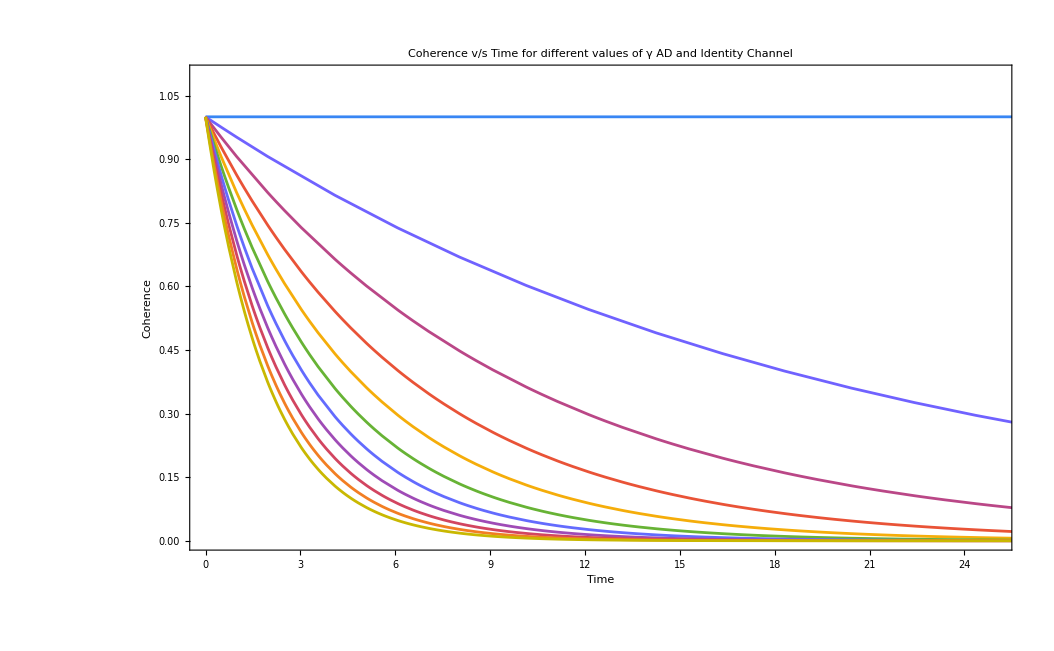

```mathematica
CoherenceT = Simplify[Abs[ρTime[[4,1]] + ρTime[[3,2]]+ρTime[[2,3]]+ρTime[[1,4]]],Element[_,Reals]];
Print["Coherence of ρ(t) =", CoherenceT]
λ = Simplify[1 - Exp[-h*t],Element[_,Reals]];

CoherenceT;


Show[Table[Plot[CoherenceT,{t,0,100},PlotRange->{{0,25},{0,1.1}},Frame->True,FrameStyle->Directive[Black,Thin],PlotStyle->ColorData[104][100*h],PlotLegends->Placed[{"γ = "<>ToString[h]},{Center,Top}],FrameLabel->{"Time","Coherence"},PlotLabel->"Coherence v/s Time for different values of γ AD and Identity Channel"],{h,0,1,0.1}]]
λ=.;
h=.;
CoherenceT=.;
```

#### Concurrence of Time Evaluated State

When amplitude damping is applied only to the Alice’s qubit of a Bell state, it results in the degradation of entanglement between the qubits and a reduction in the Concurrence.

Concurrence C(ρ(t=t)) = √(1-λ)

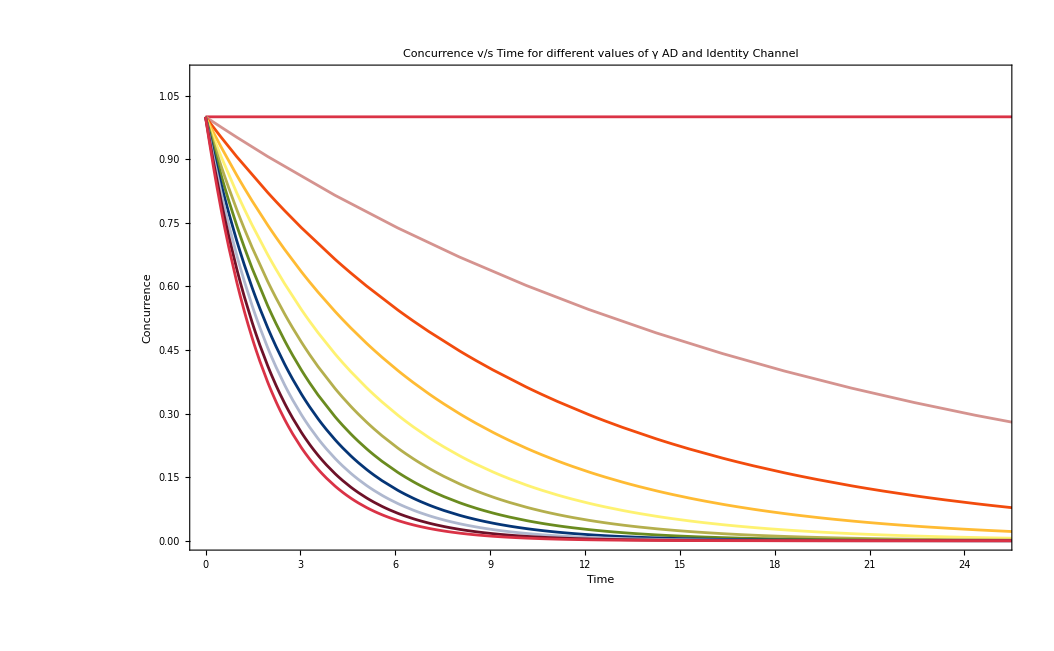

```mathematica
Subscript[σ, y] ={{0,-I},{I,0}};
Egg=KroneckerProduct[Subscript[σ, y],Subscript[σ, y]].Transpose[ρTime].KroneckerProduct[Subscript[σ, y],Subscript[σ, y]];
EgT = Sqrt[Sort[Eigenvalues[ρTime.Egg]]];
ConT = Simplify[EgT[[4]]- EgT[[3]]-EgT[[2]]-EgT[[1]]];
Print["Concurrence C(ρ(t=t)) = ", ConT]

λ = 1 - Exp[-h*t];

ConT;

Show[Table[Plot[ConT,{t,0,100},PlotRange->{{0,25},{0,1.1}},Frame->True,FrameStyle->Directive[Black,Thin],PlotStyle->ColorData[14][10*h],
PlotLegends->Placed[{"γ = "<>ToString[h]},{Center,Top}],FrameLabel->{"Time","Concurrence"},
PlotLabel->"Concurrence v/s Time for different values of γ AD and Identity Channel"],{h,0,1,0.1}]]

λ=.;
h=.;
ConT=.;
```

#### Fidelity of Time Evaluated State with State at t = 0

Fidelity of the Bell state decreases due to the loss of coherence in the first qubit induced by AD. However, the second qubit retains its coherence, and the overall Fidelity of the system is not completely lost. Instead, it is partially preserved due to the unaffected qubit. This partial preservation of Fidelity results in a mixed state with reduced Fidelity overall.
Fidelity between ρ(t=0) and ρ(t=t) is...

Fidelity f(ρ(t),ρ(0)) = 1/2 √(2+2 √(1-λ)-λ)

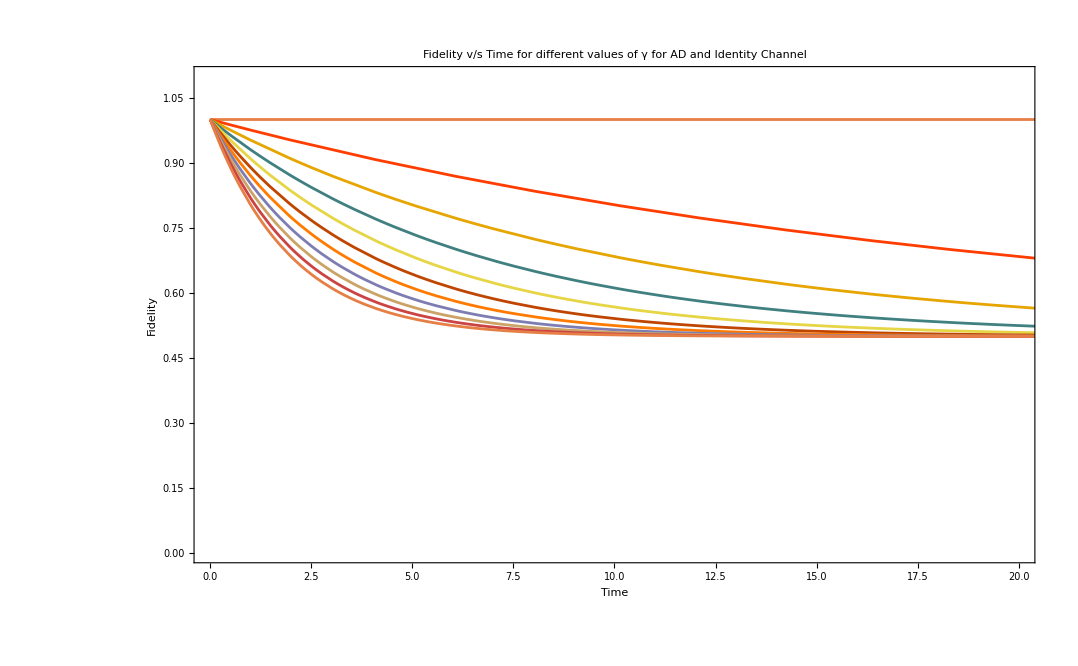

```mathematica
Fidelity = FullSimplify[Tr[MatrixPower[MatrixPower[ρZero,1/2].ρTime.MatrixPower[ρZero,1/2],1/2]]];
Print["Fidelity f(ρ(t),ρ(0)) = ",Fidelity]
λ = 1 - Exp[-h*t];

Fidelity;

Show[Table[Plot[Fidelity,{t,0,100},PlotRange->{{0,20},{0,1.1}},Frame->True,FrameStyle->Directive[Black,Thin],PlotStyle->ColorData[70][10*h],
PlotLegends->Placed[{"γ = "<>ToString[h]},{Center,Top}],FrameLabel->{"Time","Fidelity"},
PlotLabel->"Fidelity v/s Time for different values of γ for AD and Identity Channel"],{h,0,1,0.1}]]

λ=.;
h=.;
Fidelity=.;
```